# 1 - Answers to selected challenges

## Bar charts

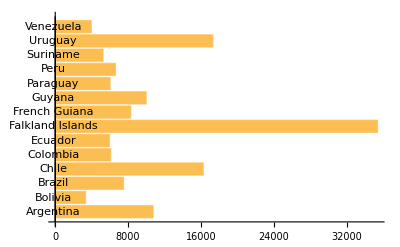

```mathematica
(* Challenge 1 *)
saCountriesM = CountryData["SouthAmerica"];
saCountries = Map[CountryData[#,"Name"]&, saCountriesM];
saGDP = Map[CountryData[#, "GDPPerCapita"]&, saCountriesM];
BarChart[saGDP, BarOrigin->Left, ChartLabels->saCountries]
```

```mathematica
(* Challenge 2 *)

lifeExpect[countr_List] := Module[
	{maleLE, femLE, countrNames},
	
	maleLE = Map[CountryData[#,"MaleLifeExpectancy"]&,
		countr];
	femLE = Map[CountryData[#,"FemaleLifeExpectancy"]&,
		countr];
	countrNames = Map[CountryData[#,"Name"]&, countr];
	
	BarChart[Transpose[{maleLE,femLE}], 
		ChartLabels->{countrNames,None},
		ChartLegends->{"male", "female"},
		BarOrigin->Left,
		PlotLabel->"Male/female Life expectancy",
		AxesLabel->{None, "years"}]
]
```

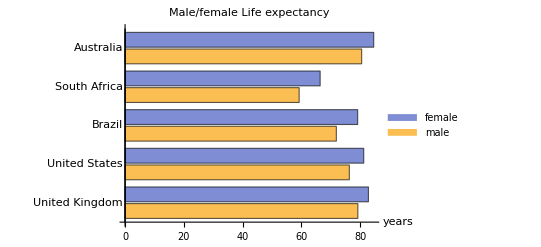

```mathematica
lifeExpect[{"UnitedKingdom","UnitedStates","Brazil",
	"SouthAfrica","Australia"}]
```

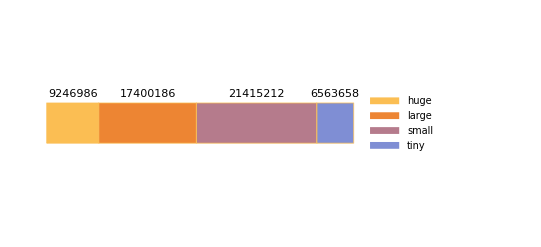

```mathematica
(* Challenege 3 *)

ukCities = CityData[{All,"UnitedKingdom"}];
ukCitiesPop = DeleteCases[Map[CityData[#,"Population"]&, ukCities],
						  _Missing] // QuantityMagnitude;
ukPopHuge = Total@Select[ukCitiesPop, # ≥ 1000000&];
ukPopLarge = Total@Select[ukCitiesPop, 100000≤#<1000000&];
ukPopSmall = Total@Select[ukCitiesPop, 10000≤#<100000&];
ukPopTiny = Total@Select[ukCitiesPop, #<10000&];

BarChart[{ukPopHuge, ukPopLarge, ukPopSmall, ukPopTiny},
	LabelingFunction->Above,
    ChartLegends->{"huge", "large", "small", "tiny"},
	BarOrigin->Left,
	ChartLayout->"Stacked",
	Axes->None]
```

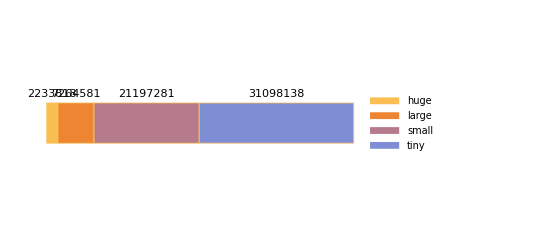

```mathematica
(* Challenge 4 *) 

cityPops[country_] := Module[
	{cities,pops,popHuge,popLarge,popSmall,popTiny},
	
	cities = CityData[{All,country}];
	pops = DeleteCases[Map[CityData[#,"Population"]&, cities],
					_Missing] // QuantityMagnitude;
	popHuge = Total@Select[pops, # ≥ 1000000&];
	popLarge = Total@Select[pops, 100000≤#<1000000&];
	popSmall = Total@Select[pops, 10000≤#<100000&];
	popTiny = Total@Select[pops, #<10000&];
	
	{popHuge, popLarge, popSmall, popTiny}
]

BarChart[cityPops["France"],
	LabelingFunction->Above,
    ChartLegends->{"huge", "large", "small", "tiny"},
	BarOrigin->Left,
	ChartLayout->"Stacked",
	Axes->None]
```

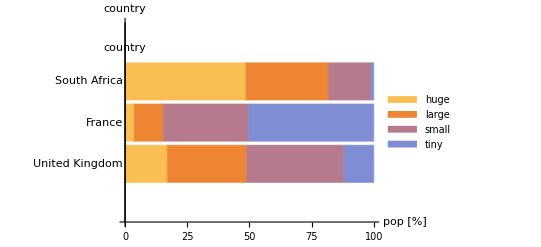

```mathematica
(* Challenge 5 *)

cityPopsChart[countries_List] :=
	BarChart[Map[cityPops, countries],
	ChartLabels->{Map[CountryData[#,"Name"]&,countries], None},
	ChartLegends->{"huge","large","small","tiny"},
	BarOrigin->Left,
	ChartLayout->"Percentile",
	AxesLabel->{"country","pop [%]"}]

cityPopsChart[{"UnitedKingdom", "France", "SouthAfrica"}]
```

## Scatter plots

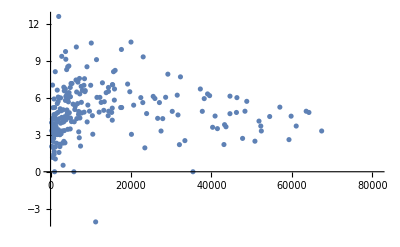

```mathematica
(* Challenge 6 - no solution shown, there
   are too many possibilities to show. Use
   common sense to choose appropriate quantities,
   and make scatter plots of life expectancy
   versus those quentities, to visualise
   correlations *)

(* Challenge 7 *)

mfDiffLE[prop_] := Module[
	{countriesM, x, y},
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, prop]&, countriesM];
	y = Map[CountryData[#, "FemaleLifeExpectancy"] - 
	        CountryData[#, "MaleLifeExpectancy"]&, countriesM];
	
	ListPlot[Transpose[{x, y}]]
]

mfDiffLE["GDPPerCapita"]zd
```

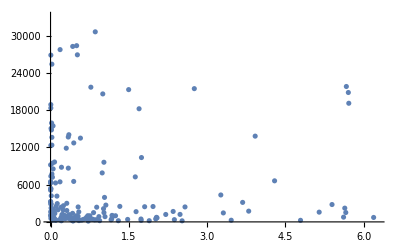

```mathematica
(* Challenge 8 *)
popgdp[year_] := Module[
	{countriesM, x, y},
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, {"Population", year}]&, countriesM];
	y = Map[CountryData[#, {"GDPPerCapita", year}]&, countriesM];
	
	ListPlot[Transpose[{x, y}]]
]

popgdp[1990]
```

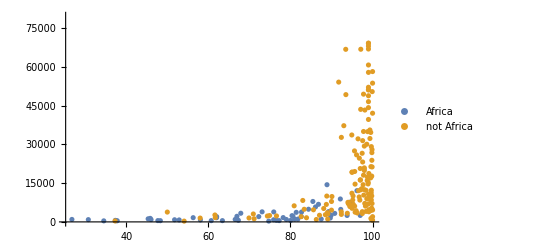

```mathematica
(* Challenge 9 *)

continentPlot[xname_, yname_, continent_] := Module[
	{countriesM, inCountries, inX, inY, 
	 outCountries, outX, outY},
	
	countriesM = CountryData["Countries"];

    inCountries = Select[countriesM, SameQ[CountryData[#,"Continent"],
					     EntityClass["Country",continent]]&];
    inX = Map[CountryData[#,xname]&, inCountries];
    inY = Map[CountryData[#,yname]&, inCountries];
    
    outCountries = Complement[countriesM, inCountries];
    outX = Map[CountryData[#,xname]&, outCountries];
    outY = Map[CountryData[#,yname]&, outCountries];
	
	ListPlot[{Transpose[{inX, inY}], 
	          Transpose[{outX, outY}]},
	         PlotLegends->{continent, Row[{"not ", continent}]}]
]

continentPlot["LiteracyRate", "GDPPerCapita", "Africa"]
```

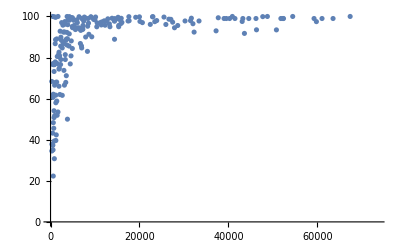

```mathematica
(* Challenge 10 *)

countryPlot1[xname_,yname_] := Module[
	{countriesM, x, y, names, ttipData, ttipPts},
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	names = Map[CountryData[#, "Name"]&, countriesM];
	
	ttipData = Transpose[{x, y, names}];
    ttipPts = Map[Tooltip[{#⟦1⟧, #⟦2⟧}, #⟦3⟧]&, ttipData]; 
	
	ListPlot[ttipPts]
]

countryPlot1["GDPPerCapita", "LiteracyRate"]
```

```mathematica
(* Challenge 11 *)

countryPlot2[xname_,yname_] := Module[
	{countriesM, x, y, flags, ttipData, ttipPts},
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	flags = Map[CountryData[#, "Flag"]&, countriesM];
	
	ttipData = Transpose[{x, y, flags}];
    ttipPts = Map[Tooltip[{#⟦1⟧, #⟦2⟧}, #⟦3⟧]&, ttipData]; 
	
	ListPlot[ttipPts]
]

countryPlot2["GDPPerCapita", "LiteracyRate"]
```

-Graphics-

```mathematica
(* Challenge 12 *)

countryPlot2[xname_,yname_] := Module[
	{countriesM, x, y, capitals, names, pops, ttipData, ttipPts},
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	capitals = Map[CountryData[#, "CapitalCity"]&, countriesM];
	names = Map[CountryData[#, "Name"]&, countriesM];
	pops = Map[CountryData[#, "Population"]&, countriesM];
	
	ttipData = Transpose[{x, y, names, capitals, pops}];
    ttipPts = Map[Tooltip[{#⟦1⟧, #⟦2⟧}, 
                          Grid[{{"Name", #⟦3⟧},
                                {"Capital", #⟦4⟧},
                                {"Pop", #⟦5⟧}}, Frame->All]]&, 
                  ttipData]; 
	
	ListPlot[ttipPts]
]

countryPlot2["GDPPerCapita", "LiteracyRate"]
```

-Graphics-

```mathematica
(* Challenge 13 *) 

(** Ignore this problem **)
```

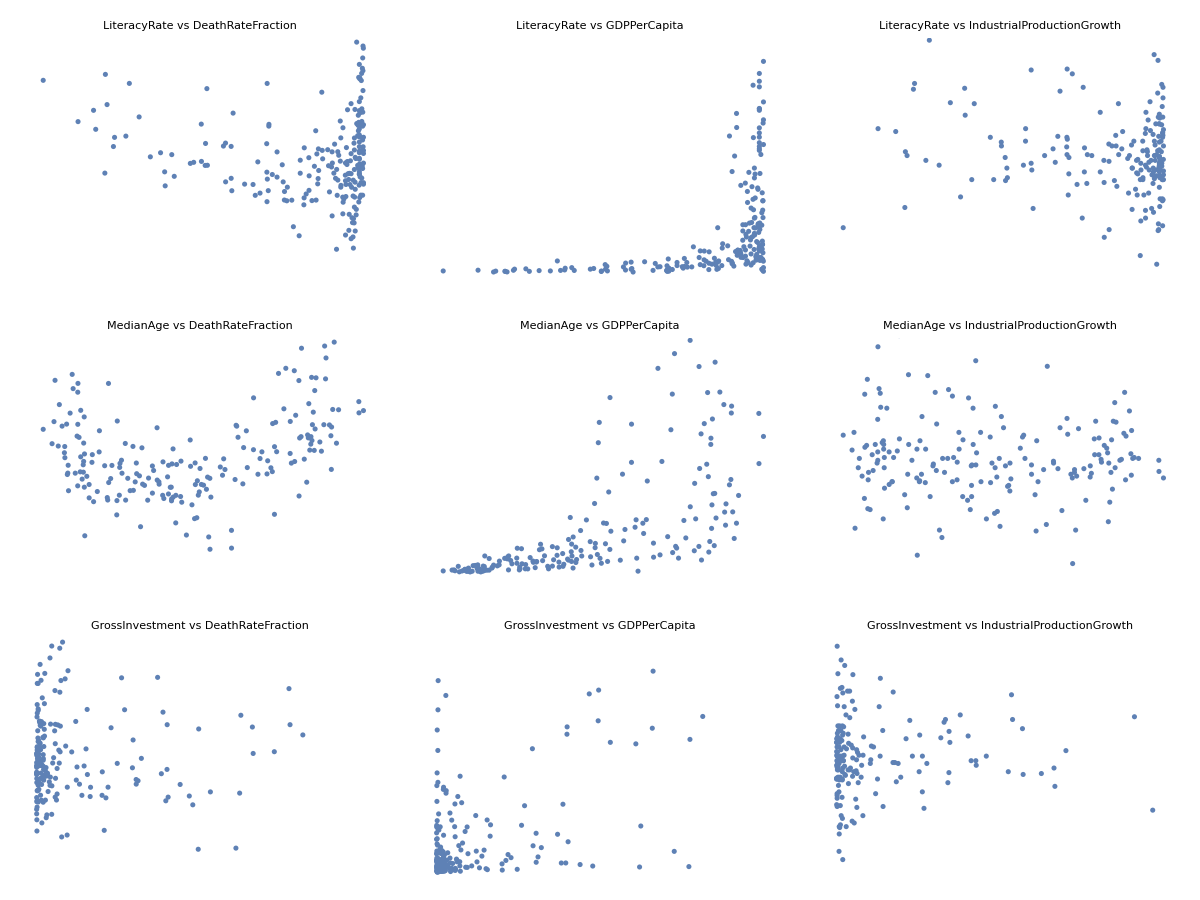

```mathematica
(* Challenge 14 *)

countryPlot[xname_,yname_, 
			opts:OptionsPattern[ListPlot]] := Module[
	{countriesM, x, y},
	
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, xname]&, countriesM];
	y = Map[CountryData[#, yname]&, countriesM];
	
	ListPlot[Transpose[{x, y}], opts]
]

gridCountryPlots[xnames_, ynames_] :=
	Grid[Table[countryPlot[xnames⟦m⟧, ynames⟦n⟧,
		PlotLabel->Row[{xnames⟦m⟧, " vs ", ynames⟦n⟧}],
		Axes->None],
	    {m, Length[xnames]}, {n, Length[ynames]}], Frame->All]
	    
gridCountryPlots[{"LiteracyRate", "MedianAge","GrossInvestment"},
                 {"DeathRateFraction", "GDPPerCapita", "IndustrialProductionGrowth"}]
```

```mathematica
(* Challenge 15*)

tabMake[props_List] :=
	TabView@Map[#->countryPlot["LiteracyRate", #,
			  AxesLabel->{"lit", #}]&,
		props]

tabMake[{"DeathRateFraction", "GDPPerCapita", "IndustrialProductionGrowth"}]
```

123

## Line plots

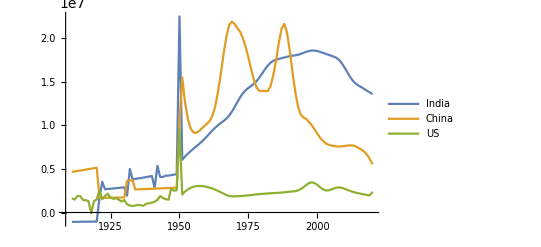

```mathematica
(* Challenge 16 *)

popsIndia = Table[CountryData["India", {"Population",y}],
                 {y, 1910,2020}];
diffsIndia = Transpose[{Range[1911,2020],Differences[popsIndia]}];
popsChina = Table[CountryData["China", {"Population",y}],
                 {y, 1910,2020}];
diffsChina = Transpose[{Range[1911,2020],Differences[popsChina]}];
popsUS = Table[CountryData["UnitedStates", {"Population",y}],
                 {y, 1910,2020}];
diffsUS = Transpose[{Range[1911,2020],Differences[popsUS]}];

ListLinePlot[{diffsIndia, diffsChina, diffsUS}, PlotLegends->{"India", "China", "US"}]
```

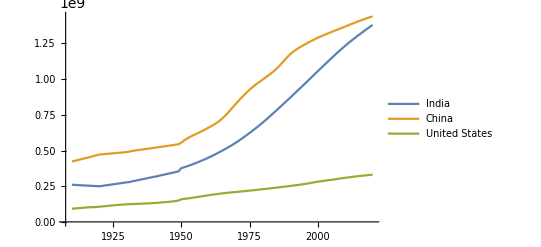

```mathematica
(* Challenge 17 *)

popCountries[nations_List] := Module[
	{pops, names},
	
	pops = Map[Table[{y,CountryData[#, {"Population",y}]},
                     {y, 1910,2020}]&,
               nations];
    names = Map[CountryData[#, "Name"]&, nations];
    ListPlot[pops, PlotLegends->names, Joined->True]
]

popCountries[{"India", "China", "UnitedStates"}]
```

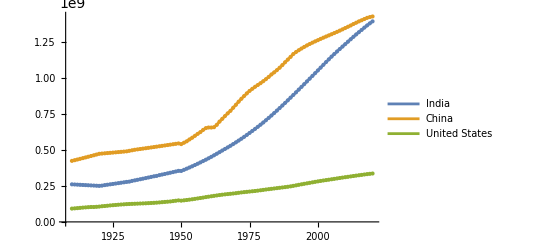

```mathematica
(* Challenge 18 *)

popCountries[nations_List] := Module[
	{pops, gdps, names, data},
	
	pops = Map[Table[{y,CountryData[#, {"Population",y}]},
                     {y, 1910,2020}]&,
               nations];
    gdps = Map[Table[CountryData[#, {"GDPPerCapita",y}],
                     {y, 1910,2020}]&,
               nations];
    names = Map[CountryData[#, "Name"]&, nations];
    data = MapThread[Tooltip, {pops, gdps}, 2];
    ListPlot[data, PlotLegends->names, Joined->True, Mesh->All]
]

popCountries[{"India", "China", "UnitedStates"}]
```

To help understand MapThread:

```mathematica
xs={a,b};
ys={c,d};
MapThread[f,{xs,ys}]
```

{f[a,c],f[b,d]}

```mathematica
xs={{Subscript[a, 1],Subscript[b, 1]},{Subscript[a, 2],Subscript[b, 2]}};
ys={{Subscript[c, 1],Subscript[d, 1]},{Subscript[c, 2],Subscript[b, 2]}};
MapThread[f,{xs,ys},2]
```

{{f[a_1,c_1],f[b_1,d_1]},{f[a_2,c_2],f[b_2,b_2]}}

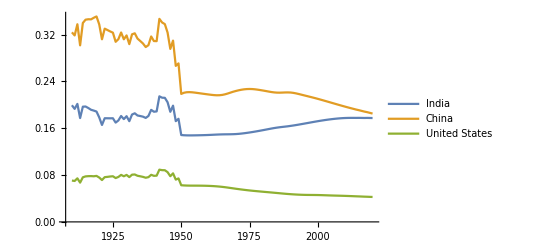

```mathematica
(* Challenge 19 *)

popPercentCountries[nations_List] := Module[
	{pops, totalPop, names},
	
	totalPop[year_] := Map[CountryData[#,{"Population",year}]&, 
	                       CountryData["Countries"]] //
		DeleteCases[#, _Missing]& //
		Total;
	pops = Map[Table[{y, CountryData[#, {"Population",y}]/totalPop[y]},
                     {y, 1910,2020}]&,
               nations];
    names = Map[CountryData[#, "Name"]&, nations];
    ListPlot[pops, PlotLegends->names, Joined->True]
]

popPercentCountries[{"India", "China", "UnitedStates"}]
```